## Code Analysis

As you continue your programming career, you will encounter larger programs that you will be tasked with understanding. And sometimes the only way to understand such large bodies of code would be to break the code into smaller snippets which you run independently to see how they behave and maybe gradually building up the larger program from this smaller snippets whenever this is possible. 
In many programming languages this might be very difficult because you will have to write a very large program to test some feature of the code you are reading but because WL is very modular you literally most of the time stitch independent pieces of code together to form a larger body of code, this tiny pieces can usually be run independently on some input and give you an idea of how they fit into the general large body of code.
We will be taking code from the note sections of Stephen Wolfram’s New Kind of Science book which contain wonderful examples of raw programming that can elevate anyone’s skill in WL programming. I personally found these code snippets useful in the development of my programming skill and I hope that it will do the same thing for you.
You might ask why we should study code that deals with abstract systems like the systems in the NKS book, this is because these pieces of code deal with “data manipulation” in the purest sense. Most of your work in programming will be about taking some data and transforming it in various ways, be it numeric data, textual data, images or videos, at the bottom line all higher forms of data are actually handled as numbers by a computer. A computer only knows how to handle numbers. So with these programs from the NKS books we handle data transformation at its core level and develop skills we can apply for the rest of our programming career. The original code samples are available at www.wolframscience.com

```mathematica
centerList[n_Integer]:=ReplacePart[Table[0,n],1,Ceiling[n/2]]
```

```mathematica
centerList[11]
```

{0,0,0,0,0,1,0,0,0,0,0}

To analyse this program we will have to break it up in parts and see what each part does. This is essentially the way I will do it but you are free to do it in your own style.
What the program does essentially is to put a 1 in the middle of a list of Os. In order to have a list balanced, i.e. has an equal number of 0s on both sides of the 1s we call the function with an odd Integer as argument.

```mathematica
centerList[10]
```

{0,0,0,0,1,0,0,0,0,0}

As we can see with an even number the list is unbalanced and has more 0s on the left than on the right.

```mathematica
Table[0,11]
```

{0,0,0,0,0,0,0,0,0,0,0}

From the program above we see that we pass a variable n into the program with head Integer. we use the n within the expression twice, once to get a list of 0s of length n and in the second case:

```mathematica
Ceiling[11/2]
```

6

We use the ceiling function to find a mid point in the list of zeros. If we divide n/2 without the ceiling function this is what we get

```mathematica
11/2
```

11/2

```mathematica
N[11/2]
```

5.5

We use the Ceiling function to find the next Integer after 5.5 which is 6. Another function you will see in many programs is the

```mathematica
Floor[N[11/2]]
```

5

Which is the previous Integer before 5.5 ReplacePart replaces the 0 at the index provided by Ceiling with a 1 and hence the final output.

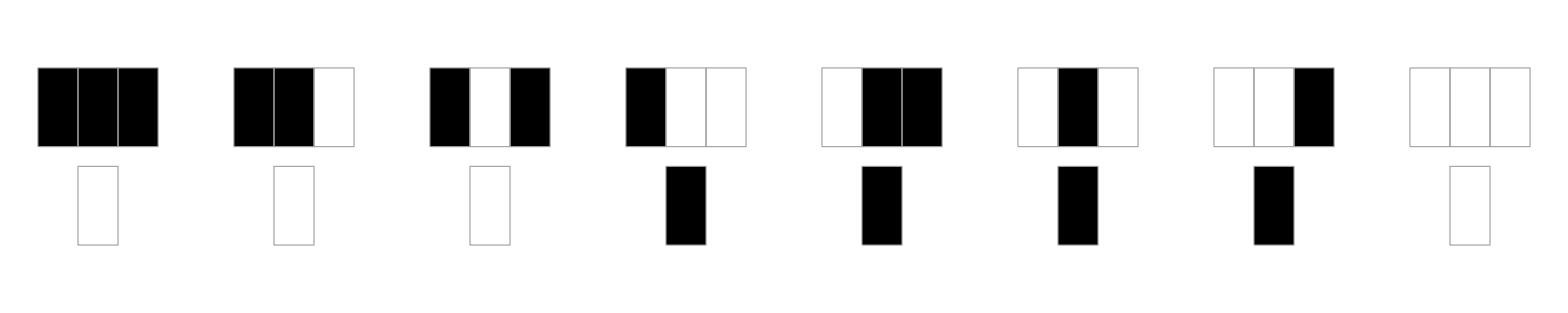

```mathematica
RulePlot[CellularAutomaton[30]]
```

A CellularAutomaton is a abstract computational system or machine, that receives an Input of a Rule number and a initialization list representing a state and performs some fixed transformation on this initial list by applying the rule.

Above is a graphic produced by the function RulePlot which is applied to the elementary CellularAutomaton Rule 30. What the plot essentially states is a simple transformation formula, Black represents 1 and White represents white. The Rule states that wherever we have 3 whites we should replace it with white and whenever we have 3 blacks we replace it with a white. The first row is the the input while the second row is the output given the input. So why again are we dealing with CellularAutomatons? Like I said we are learning how to manipulate data, which is an essential skill in any programming enterprise. In this case we handle the data as a List and use certain functions to manipulate the data towards our goals.

Rule 30 is just one of the 256 Elementary CellularAutomatons available

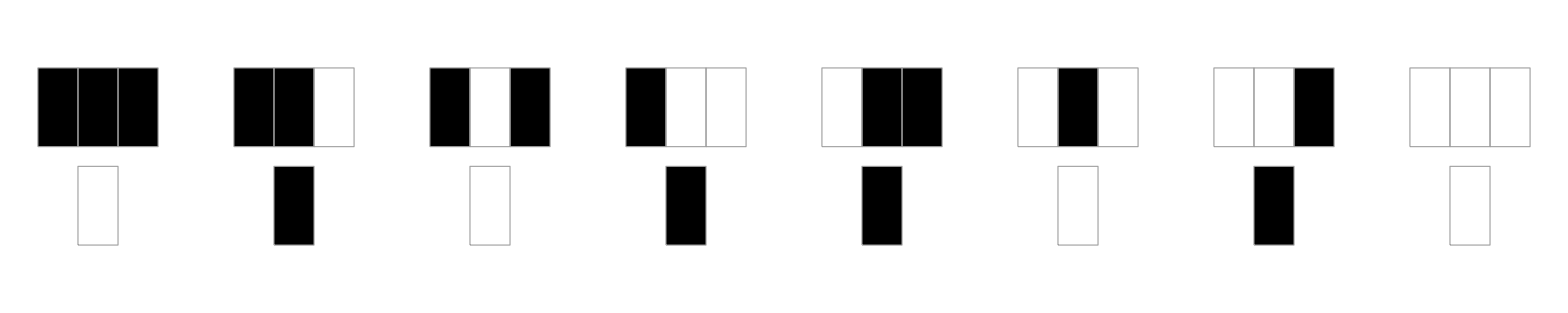

```mathematica
RulePlot[CellularAutomaton[90]]
```

Rule 90 is another and we see that in Rule 90 the individual output from the first row differs somewhat from that of Rule 30. In this case where in Rule 30 we had Black Black White -> White or {1,1,0} -> 0 in Rule 90 we have {1,1,0} -> 1

```mathematica
{Black, Black, White} -> Black
```

{GrayLevel[0],GrayLevel[0],GrayLevel[1]}→GrayLevel[0]

In WL we can directly represent colors by their names and we can see in the program above we create a Rule that maps 3 colors in a list that could be taken to represent {1,1,0} to a color Black that could be taken to represent 1 this is just a convention that enables us to express certain ideas and is not a hard and fast rule.

Apart from CellularAutomatons there are other computational system like Turing Machines, Mobile Automatons, Register Machines, Substitution systems, Multiway systems etc. To explore these systems in full you will have to read the NKS book available at www.wolframscience.com

```mathematica
Tuples[{1,0},3]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

If we look at the top row of RulePlot from which we transform each triple color or number to a single number in to bottom row, we can see that there is a WL built-in function that generates all the possible combinations of black and white up to length 3. From binary numbers we know that if we allow 3 binary digits we can enumerate the first 8 Integers start from 0 in the tenary number system. Each triple above can be converted to it’s tenary representative

```mathematica
Map[FromDigits[#,2]&,Tuples[{1,0},3]]
```

{7,6,5,4,3,2,1,0}

So we see that each triple just corresponds to one Integer from 0 to 7. In the program above we Map a pure function over each triple generated by Tuple[{1,0},3]. Another way to Map a function over a bunch of inputs is to use the slash at /@. Using this we perform the above action again:

```mathematica
FromDigits[#,2]&/@Tuples[{1,0},3]
```

{7,6,5,4,3,2,1,0}

There is also a function to obtain the output, i.e. the second row from the RulePlot function

```mathematica
IntegerDigits[30,2,8] (* Rule 30 above *)
```

{0,0,0,1,1,1,1,0}

```mathematica
IntegerDigits[90,2,8]
```

{0,1,0,1,1,0,1,0}

Using these foundational programming constructs we can now create our own primitive version of RulePlot. This is a very hacky version which I would recommend not to use for any serious work. It is merely to demonstrate some features of the WL, and to also show that we can emulate most of the built in functionality in WL. It is always recommended to use built in functions whenever possible because they have gone through a lot of rigorous testing.

```mathematica
Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] (* The input row above *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]]
```

{0,0,0,1,1,1,1,0}

```mathematica
Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]/.{0->White, 1-> Black}]
```

{GrayLevel[1],GrayLevel[1],GrayLevel[1],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[1]}

```mathematica
Transpose[{Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] ,Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]/.{0->White, 1-> Black}]  }] (* Pair Input row to result row *)
```

{{-Graphics-,GrayLevel[1]},{-Graphics-,GrayLevel[1]},{-Graphics-,GrayLevel[1]},{-Graphics-,GrayLevel[0]},{-Graphics-,GrayLevel[0]},{-Graphics-,GrayLevel[0]},{-Graphics-,GrayLevel[0]},{-Graphics-,GrayLevel[1]}}

```mathematica
Map[GraphicsColumn,Transpose[{Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] ,Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]/.{0->White, 1-> Black}]  }] ](* Arrange input and output in a single column *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[Map[GraphicsColumn,Transpose[{Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] ,Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]/.{0->White, 1-> Black}]  }] ], Frame->All](* Put everything in a GraphicsRow with a Frame around everything *)
```

-Graphics-

```mathematica
Rasterize[GraphicsRow[Map[GraphicsColumn,Transpose[{Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] ,Map[Row[{"",#,""}]&,IntegerDigits[30,2,8]/.{0->White, 1-> Black}]  }] ], Frame->All]](* Rasterize to turn it into a single image *)
```

-Graphics-

```mathematica
myRulePlot[rule_Integer]:=Rasterize[GraphicsRow[Map[GraphicsColumn,Transpose[{Map[ArrayPlot[{#},Mesh->All,ImageSize->30]&,Tuples[{1,0},3]] ,Map[Row[{"",#,""}]&,IntegerDigits[rule,2,8]/.{0->White, 1-> Black}]  }] ], Frame->All]](* We wrap everything in a function so we can generalize for any of the elementary CA rules *)
```

```mathematica
(* We test below using Rules 45 and 90 *) 
myRulePlot[45]
```

-Graphics-

```mathematica
myRulePlot[90]
```

-Graphics-

Now that we have seen how to emulate the RulePlot builtin function we shall go further to analyse other CA based program and expand both our programming vocabulary and skillset.

```mathematica
elementaryRule[num_Integer]:= IntegerDigits[num,2,8]
```

We abstract away our elementary rule generation expression into a function so we can incorporate it into other functions.

```mathematica
caStep[rule_List,a_List]:=rule⟦8-(RotateLeft[a]+2 (a+2 RotateRight[a]))⟧
```

The caStep function above receives a rule list and an input list and performs one step in an elementary cellular automaton evolution. Lets tear it apart so we could see how it ticks. But first lets run it to see some output:

```mathematica
caStep[elementaryRule[30],centerList[11]]
```

{0,0,0,0,1,1,1,0,0,0,0}

```mathematica
inputList = centerList[11]
```

{0,0,0,0,0,1,0,0,0,0,0}

```mathematica
RotateRight[inputList] (* Rotate list one step to the right *)
```

{0,0,0,0,0,0,1,0,0,0,0}

```mathematica
2 RotateRight[inputList] (* Multiply whole list by 2 *)
```

{0,0,0,0,0,0,2,0,0,0,0}

```mathematica
inputList + 2 RotateRight[inputList] (* add initial list to the last result *)
```

{0,0,0,0,0,1,2,0,0,0,0}

```mathematica
2(inputList + 2 RotateRight[inputList]) (* Multiply everything by 2 again *)
```

{0,0,0,0,0,2,4,0,0,0,0}

```mathematica
RotateLeft[inputList] (* Rotate original inputlist to the left *)
```

{0,0,0,0,1,0,0,0,0,0,0}

```mathematica
RotateLeft[inputList] + 2(inputList + 2 RotateRight[inputList])
```

{0,0,0,0,1,2,4,0,0,0,0}

```mathematica
elementaryRule[30][[8-(RotateLeft[inputList] +2(inputList + 2 RotateRight[inputList])) ]]
```

{0,0,0,0,1,1,1,0,0,0,0}